```mathematica
Import["GraphPartition.m"]
<< GraphPartition`
(*<<Combinatorica`*)
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
ga=RoachGraph[4];
ShowGraph[ga]
```

ShowGraph[⁃Graph:<8,8,Undirected>⁃]

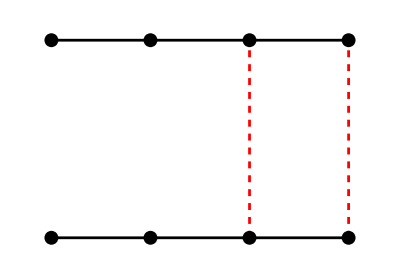

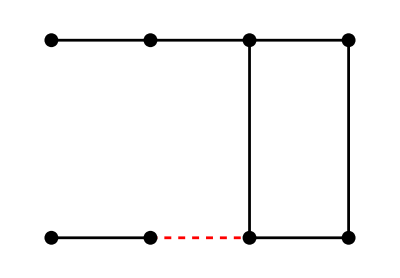

MultipleFiedlerVector[⁃Graph:<8,8,Undirected>⁃]

MultipleFiedlerVector

```mathematica
GraphPartition`ShowSpectralCut[ga]
GraphPartition`ShowIsoperimetricCut[SetVertexWeights[ga,Table[1,8]]]

GraphPartition`MultipleFiedlerVector[SetVertexWeights[ga,Table[1,8]]]
```